## Magnetic field

```mathematica
(* Modified 𝔹 in the interior of the magnet which should be multiplied by preFactor=2/3*μ0*M01 ... *)
(* In spherical eigen-coordinates AND spherical eigen-components *)
𝔹InnerSph[r_,ϑ_,φ_]:={Cos[ϑ],-Sin[ϑ],0};
𝔹OuterSph[r_,ϑ_,φ_]:=1/r^3*{Cos[ϑ],1/2*Sin[ϑ],0};
(* in eigen-cartesian basis and eigen-cartesian coordinates *)

(* Spherical basis vectors in the eigen system (both, coordinates and directions) *)
𝕖r[ϑ_,φ_]:={Sin[ϑ]*Cos[φ],Sin[ϑ]*Sin[φ],Cos[ϑ]};
𝕖ϑ[ϑ_,φ_]:={Cos[ϑ]*Cos[φ],Cos[ϑ]*Sin[φ],-Sin[ϑ]};
𝕖φ[ϑ_,φ_]:={-Sin[φ],Cos[φ],0};

𝔹InnerCart[x_,y_,z_]:=(
{0,0,1}
);
𝔹OuterCart[x_,y_,z_]:=(
rVal=Sqrt[x^2+y^2+z^2];
ϑVal=ArcTan[z,Sqrt[x^2+y^2]];
φVal=ArcTan[x,y];
{Br,Bϑ,Bφ}=𝔹OuterSph[rVal,ϑVal,φVal];
Br*𝕖r[ϑVal,φVal]+Bϑ*𝕖ϑ[ϑVal,φVal]+Bφ*𝕖φ[ϑVal,φVal]
);
```

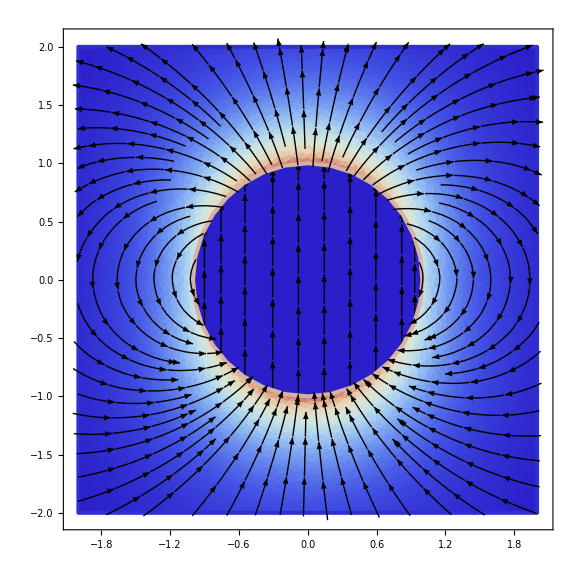

```mathematica
ballMagnet=Disk[];
ballMagnetBoundary=Circle[];
canvas=Rectangle[{-2,-2},{2,2}];
BplotOuter[y0_,z0_]=𝔹OuterCart[0,y0,z0][[{2,3}]];
outerPlot=StreamDensityPlot[Evaluate@BplotOuter[y0,z0],{y0,z0}∈RegionDifference[canvas,ballMagnet],ColorFunction->ColorData["ThermometerColors"], StreamStyle->Black,StreamColorFunction->None,AspectRatio->Automatic,BoundaryStyle->{Black,Thickness[0.005]}];
BplotInner[y0_,z0_]=𝔹InnerCart[0,y0,z0][[{2,3}]];
innerPlot=StreamDensityPlot[Evaluate@BplotInner[y0,z0],{y0,z0}∈ballMagnet,ColorFunction->ColorData["ThermometerColors"],StreamStyle->Black,StreamColorFunction->None,StreamPoints->10,StreamScale->0.12,AspectRatio->Automatic,BoundaryStyle->{Black,Thickness[0.005]}];
ballMagnetPlot=Show[innerPlot,outerPlot,PlotRange->All,ImageSize->Large]
```

```mathematica
Export["ballMagnet.pdf",ballMagnetPlot]
```

ballMagnet.pdf

## Force between spherical magnets

```mathematica
(* Magnetic field *)
B=2/3*mu0*M01*(r/R1)^(-3)*{Cos[ϑ],Sin[ϑ]/2,0};
```

Force will be computed following: https://aapt.scitation.org/doi/10.1119/1.4973409

```mathematica
gradB=Grad[B,{r,ϑ,φ},"Spherical"]//Expand;
```

```mathematica
(*volume of second times gradient gives some rhs. the solution is obtained by multiplying the other magnet's magnetization vector from the left *)
V2=4/3*π*R2^3;
rhs=V2*gradB;
```

```mathematica
factor = 4/3*mu0*M01*π/r^4*(R1*R2)^3
```

(4 M01 mu0 π R1^3 R2^3)/(3 r^4)

```mathematica
rhs/factor//Simplify
```

{{-2 Cos[ϑ],-Sin[ϑ],0},{-Sin[ϑ],Cos[ϑ],0},{0,0,Cos[ϑ]}}

The force is simply given by F = M2 * rhs. The factor can be written in front.

```mathematica
(* transformation matrix from spherical to cartesian basis *)
Q={
{Sin[ϑ]*Cos[φ],Sin[ϑ]*Sin[φ],Cos[ϑ]},
{Cos[ϑ]*Cos[φ],Cos[ϑ]*Sin[φ],-Sin[ϑ]},
{-Sin[φ],Cos[φ],0}
}
```

{{Cos[φ] Sin[ϑ],Sin[ϑ] Sin[φ],Cos[ϑ]},{Cos[ϑ] Cos[φ],Cos[ϑ] Sin[φ],-Sin[ϑ]},{-Sin[φ],Cos[φ],0}}

#### Special case: phi = pi/2

```mathematica
(* assume a magnetization M2 of a special form (in cartesian basis of first magnet) *)
M2=M02*{0,-Sin[ζ],Cos[ζ]};
(* compute force in cartesian coordinates of first magnet *)
F=M2.Qᵀ.rhs.Q//Simplify
FInPlane=F/.φ->π/2
```

{-(2 M01 M02 mu0 π R1^3 R2^3 Cos[φ] Sin[ϑ] (Cos[ζ] (3+5 Cos[2 ϑ])-5 Sin[ζ] Sin[2 ϑ] Sin[φ]))/(3 r^4),-(4 M01 M02 mu0 π R1^3 R2^3 (4 Cos[ζ] Cos[ϑ]^2 Sin[ϑ] Sin[φ]-Cos[ζ] Sin[ϑ]^3 Sin[φ]+Cos[ϑ]^3 Sin[ζ] Sin[φ]^2+Cos[ϑ] Sin[ζ] (Cos[φ]^2-4 Sin[ϑ]^2 Sin[φ]^2)))/(3 r^4),-(M01 M02 mu0 π R1^3 R2^3 (Cos[ζ] (3 Cos[ϑ]+5 Cos[3 ϑ])-2 (3+5 Cos[2 ϑ]) Sin[ζ] Sin[ϑ] Sin[φ]))/(3 r^4)}

{0,-(4 M01 M02 mu0 π R1^3 R2^3 (Cos[ϑ]^3 Sin[ζ]+4 Cos[ζ] Cos[ϑ]^2 Sin[ϑ]-4 Cos[ϑ] Sin[ζ] Sin[ϑ]^2-Cos[ζ] Sin[ϑ]^3))/(3 r^4),-(M01 M02 mu0 π R1^3 R2^3 (Cos[ζ] (3 Cos[ϑ]+5 Cos[3 ϑ])-2 (3+5 Cos[2 ϑ]) Sin[ζ] Sin[ϑ]))/(3 r^4)}

```mathematica
factor=-1/3/r^4*M01*M02*mu0*π*R1^3*R2^3
```

-(M01 M02 mu0 π R1^3 R2^3)/(3 r^4)

```mathematica
FInPlane/factor//Simplify
```

{0,-Sin[ζ-ϑ]+5 Sin[ζ+3 ϑ],Cos[ζ-ϑ]+2 Cos[ζ+ϑ]+5 Cos[ζ+3 ϑ]}

```mathematica
FInPlane/factor/.ϑ->η+π/2//Simplify
```

{0,Cos[ζ-η]-5 Cos[ζ+3 η],Sin[ζ-η]-2 Sin[ζ+η]+5 Sin[ζ+3 η]}

#### Special case: phi = pi/2, theta=pi/2

```mathematica
(* compute force in cartesian coordinates of first magnet *)
F=M2.Qᵀ.rhs.Q//Simplify
F/.{φ->π/2,ϑ->π/2}//Simplify
```

{-(2 M01 M02 mu0 π R1^3 R2^3 Cos[φ] Sin[ϑ] (Cos[ζ] (3+5 Cos[2 ϑ])-5 Sin[ζ] Sin[2 ϑ] Sin[φ]))/(3 r^4),-(4 M01 M02 mu0 π R1^3 R2^3 (4 Cos[ζ] Cos[ϑ]^2 Sin[ϑ] Sin[φ]-Cos[ζ] Sin[ϑ]^3 Sin[φ]+Cos[ϑ]^3 Sin[ζ] Sin[φ]^2+Cos[ϑ] Sin[ζ] (Cos[φ]^2-4 Sin[ϑ]^2 Sin[φ]^2)))/(3 r^4),-(M01 M02 mu0 π R1^3 R2^3 (Cos[ζ] (3 Cos[ϑ]+5 Cos[3 ϑ])-2 (3+5 Cos[2 ϑ]) Sin[ζ] Sin[ϑ] Sin[φ]))/(3 r^4)}

{0,(4 M01 M02 mu0 π R1^3 R2^3 Cos[ζ])/(3 r^4),-(4 M01 M02 mu0 π R1^3 R2^3 Sin[ζ])/(3 r^4)}

```mathematica
factorSpecial=4/3*mu0*M01*M02*π*(R1*R2)^3/r^4
F/factorSpecial//Simplify
```

(4 M01 M02 mu0 π R1^3 R2^3)/(3 r^4)

{-1/2 Cos[φ] Sin[ϑ] (Cos[ζ] (3+5 Cos[2 ϑ])-5 Sin[ζ] Sin[2 ϑ] Sin[φ]),-4 Cos[ζ] Cos[ϑ]^2 Sin[ϑ] Sin[φ]+Cos[ζ] Sin[ϑ]^3 Sin[φ]-Cos[ϑ]^3 Sin[ζ] Sin[φ]^2-Cos[ϑ] Sin[ζ] (Cos[φ]^2-4 Sin[ϑ]^2 Sin[φ]^2),1/4 (-Cos[ζ] (3 Cos[ϑ]+5 Cos[3 ϑ])+2 (3+5 Cos[2 ϑ]) Sin[ζ] Sin[ϑ] Sin[φ])}

## Torque between spherical magnets

```mathematica
xM2=Qᵀ.{r,0,0};
tau=V2*M2×(Qᵀ.B)//Simplify
```

{-(4 M01 M02 mu0 π R1^3 R2^3 (2 Cos[ϑ]^2 Sin[ζ]-Sin[ζ] Sin[ϑ]^2+3 Cos[ζ] Cos[ϑ] Sin[ϑ] Sin[φ]))/(9 r^3),(4 M01 M02 mu0 π R1^3 R2^3 Cos[ζ] Cos[ϑ] Cos[φ] Sin[ϑ])/(3 r^3),(4 M01 M02 mu0 π R1^3 R2^3 Cos[ϑ] Cos[φ] Sin[ζ] Sin[ϑ])/(3 r^3)}

```mathematica
factor=4 M01 mu0 π/3/r^3 R1^3 R2^3
V2*(Qᵀ.B)/factor//Simplify
```

(4 M01 mu0 π R1^3 R2^3)/(3 r^3)

{Cos[ϑ] Cos[φ] Sin[ϑ],Cos[ϑ] Sin[ϑ] Sin[φ],1/6 (1+3 Cos[2 ϑ])}

```mathematica
factorSpecial=4/3*mu0*M01*M02*π*(R1*R2)^3/r^3;
tau/factorSpecial//Simplify
```

{1/3 (-2 Cos[ϑ]^2 Sin[ζ]+Sin[ζ] Sin[ϑ]^2-3 Cos[ζ] Cos[ϑ] Sin[ϑ] Sin[φ]),Cos[ζ] Cos[ϑ] Cos[φ] Sin[ϑ],Cos[ϑ] Cos[φ] Sin[ζ] Sin[ϑ]}

The torque can be computed from the force. Again, consider the special case: phi = pi/2, theta=pi/2

```mathematica
tau/.{φ->π/2,ϑ->η+π/2}//Simplify
```

{-(2 M01 M02 mu0 π R1^3 R2^3 (Sin[ζ]-3 Sin[ζ+2 η]))/(9 r^3),0,0}

The torque can be computed from the force. Again, consider the special case: phi = pi/2, theta=pi/2

```mathematica
tau/.{φ->π/2,ϑ->π/2}//Simplify
```

{(4 M01 M02 mu0 π R1^3 R2^3 Sin[ζ])/(9 r^3),0,0}